```mathematica
SetDirectory[NotebookDirectory[]];data=ArrayReshape[#,{100,200}]&@BinaryReadList["./dk.dat","Real32"];
j0=BinaryReadList["./j0.dat","Real32"];
freq=BinaryReadList["./freq.dat","Real32"];
coef=ArrayReshape[#,{200,200}]&@BinaryReadList["./coef.dat","Real32"];
(*ListLinePlot[Append[Table[data[[1;;200,k]],{k,400,150,-10}],Table[45,{n,1,200}]],PlotLegends->Automatic,PlotRange->All]*)
```

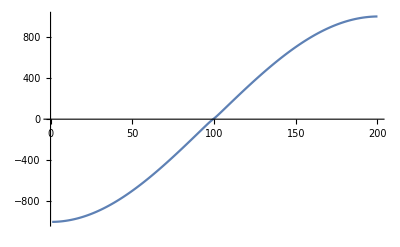

```mathematica
ListLinePlot[freq,PlotLegends->Automatic,PlotRange->All]
```

```mathematica
Animate[ListLinePlot[data[[t]],PlotLegends->Automatic,PlotRange->{{0,200},{0,300}}],{t,1,100,1},AnimationRate->2,RefreshRate->30]
```

```mathematica
ListLinePlot[Table[data[[t]],{t,1,200,20}],PlotRange->All]
```

Part::partw: Part 101 of {{0.,0.,8.88178×10^-16,4.44089×10^-16,6.66134×10^-16,1.9984×10^-15,3.88578×10^-15,1.9984×10^-15,1.66533×10^-15,6.66134×10^-16,«190»},«9»,«90»} does not exist.

Part::partw: Part 121 of {{0.,0.,8.88178×10^-16,4.44089×10^-16,6.66134×10^-16,1.9984×10^-15,3.88578×10^-15,1.9984×10^-15,1.66533×10^-15,6.66134×10^-16,«190»},«9»,«90»} does not exist.

Part::partw: Part 141 of {{0.,0.,8.88178×10^-16,4.44089×10^-16,6.66134×10^-16,1.9984×10^-15,3.88578×10^-15,1.9984×10^-15,1.66533×10^-15,6.66134×10^-16,«190»},«9»,«90»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{{1.,0.},{2.,0.},{3.,8.88178×10^-16},{4.,4.44089×10^-16},{5.,6.66134×10^-16},{6.,1.9984×10^-15},{7.,3.88578×10^-15},{8.,1.9984×10^-15},{9.,1.66533×10^-15},{10.,6.66134×10^-16},«190»},«8»,{}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{0.,0.,8.88178×10^-16,4.44089×10^-16,6.66134×10^-16,1.9984×10^-15,3.88578×10^-15,1.9984×10^-15,1.66533×10^-15,183,2.23294×10^-14,5.04319×10^-14,6.09929×10^-15,4.04884×10^-14,2.58682×10^-14,4.52277×10^-14,3.0035×10^-14,75.6897},8,1},1]
 |  |  |  |

```mathematica
Sum[data[[1,i]],{i,1,200}]
```

334.849

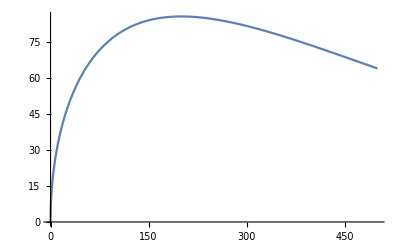

```mathematica
Plot[Sqrt[100*Abs[x] E^(- Abs[x]/200)],{x,0,500},PlotRange->Full]
```

```mathematica
Manipulate[ListLinePlot[coef[[n,All]],PlotRange->Full],{n,1,200,1}]
```

```mathematica
ΔH=-0.0964;u22={0.0958,-0.7722,0.1177};u11={-27.6663,-5.9275,1.2562};u12={0.48725267,0.089372,-0.03379048}/0.393430307;
u12v = u12.(u11-u22)/Norm[u11-u22];
hab = Abs[u12v*ΔH]/(√(Norm[u11-u22]^2+4 u12v^2))
```

0.00428644

```mathematica
ΔH=1.0748;u22={0,0,0};u11={-21.0298,-6.7092,2.1952};u12={-0.06718129,-0.15142017,0.03728061}/0.393430307;
u12v = (u12.(u11-u22))/Norm[u11-u22];
hab = Abs[u12v*ΔH]/(√(Norm[u11-u22]^2+4 u12v^2))
```

0.013933

```mathematica
ΔH=-0.0964;u22={0.0958,-0.7722,0.1177};u11={-27.6663,-5.9275,1.2562};u12={0.48725267,0.089372,-0.03379048}/0.393430307;
u12v = Norm[u12];
hab = Abs[u12v*ΔH]/(√(Norm[u11-u22]^2+4 u12v^2))
```

0.0042881

```mathematica
ΔH=1.0748;u22={0,0,0};u11={-21.0298,-6.7092,2.1952};u12={-0.06718129,-0.15142017,0.03728061}/0.393430307;
u12v = Norm[u12];
hab = Abs[u12v*ΔH]/(√(Norm[u11-u22]^2+4 u12v^2))
```

0.020895

```mathematica
ΔH=-0.1288;u22={-1.141,-0.9247,-0.6088};u11={-25.3102,-6.2400,-3.7840};u12={-1.11959105,-0.28161743,-0.16122694}/0.393430307;
u12v =  (u12.(u11-u22))/Norm[u11-u22];
hab = Abs[u12v*ΔH]/(√(Norm[u11-u22]^2+4 u12v^2))
```

0.0148743

```mathematica
ΔH=-0.1288;u22={-1.141,-0.9247,-0.6088};u11={-25.3102,-6.2400,-3.7840};u12={-1.11959105,-0.28161743,-0.16122694}/0.393430307;
u12v = Norm[u12];
hab = Abs[u12v*ΔH]/(√(Norm[u11-u22]^2+4 u12v^2))
```

0.0148814

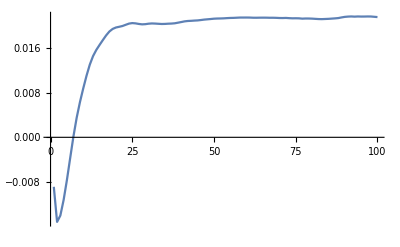
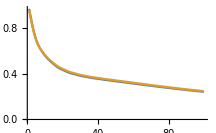
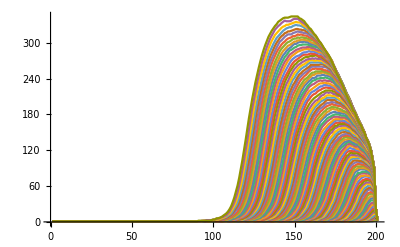
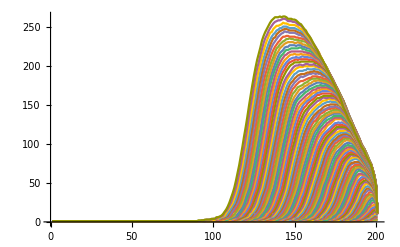

```mathematica
SetDirectory[NotebookDirectory[]];numMode =200;numStep=100;pop=BinaryReadList["./pop.dat","Real32"];num=ArrayReshape[#,{numStep,200}]&@BinaryReadList["./num_ic.dat","Real32"];
dim=ArrayReshape[#,{numStep,numMode+1}]&@BinaryReadList["./dim.dat","Real32"];popSh=BinaryReadList["./pop_sh.dat","Real32"];
dimSh=ArrayReshape[#,{numStep,numMode+1}]&@BinaryReadList["./dim_sh.dat","Real32"];{ListLinePlot[(pop-popSh)/pop,PlotRange->Full],ListLinePlot[{popSh,pop},PlotRange->Full],ListLinePlot[dim[[1;;numStep;;1,All]],PlotRange->All],ListLinePlot[dimSh[[1;;numStep;;1,All]],PlotRange->All]}
```

```mathematica
Length[%]
```

2

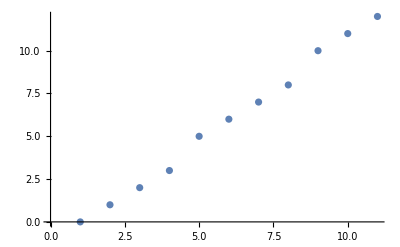

```mathematica
ListPlot[Table[Floor[n/0.8],{n,0,10}]]
```

```mathematica
N[Integrate[Sin[x],{x,1,2}]-5Integrate[Sin[x],{x,1/5,2/5}]]
```

0.661421

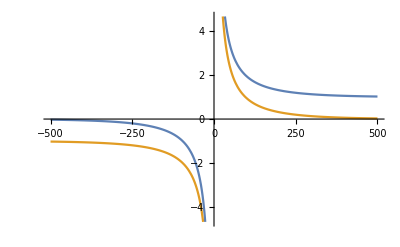

```mathematica
Plot[{1/2(1+Coth[(w/2)/(0.695 *200)]),-1/2(1+Coth[(-w/2)/(0.695 *200)])},{w,-500,500}]
```

```mathematica
√(1/2(1+Coth[x]))
```

```mathematica
Simplify[(√(1+Coth[x]))/(√2)]
```

(√(1+Coth[x]))/(√2)

```mathematica
TrigToExp[(√(1+Coth[x/2]))/(√2)]
```

(√(1+(ⅇ^(-x/2)+ⅇ^(x/2))/(-ⅇ^(-x/2)+ⅇ^(x/2))))/(√2)

```mathematica
Simplify[(√(1+(ⅇ^(-x/2)+ⅇ^(x/2))/(-ⅇ^(-x/2)+ⅇ^(x/2))))/(√2)]
```

√(ⅇ^x/(-1+ⅇ^x))

```mathematica
ΔH=-0.0964;u22={0.0958,-0.7722,0.1177};u11={-27.6663,-5.9275,1.2562};u12={0.48725267,0.089372,-0.03379048}/0.393430307;
u12v = Norm[u12];
hab = 1/(2 √2)(√(1+(u12v^2-Norm[u11-u22]^2/4)/(√((u12v^2-Norm[u11-u22]^2/4)^2+(u12.(u11-u22))^2))))ΔH
```

-0.00428647

```mathematica
{0.48725267,0.089372,-0.03379048}/0.393430307
```

{1.23847,0.227161,-0.0858868}

```mathematica
drude[w_,lam_,gam_]:=2*lam*gam*w/(w^2+gam^2);
```

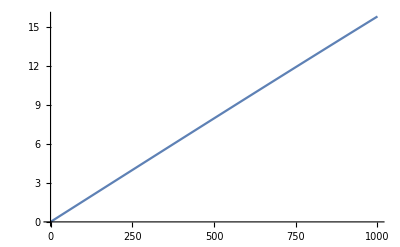

```mathematica
Plot[drude[w,80,10000],{w,0,1000}]
```